```mathematica
Compute2DShape[order_,eltype_]:=Block[{zeta1,zeta2,zeta3,a,b,xi,eta,psis,dpsis},
If[eltype==1,
If[order==1,
psis={
1/4(1-xi)(1-eta),
1/4(1+xi)(1-eta),
1/4 (1+xi)(1+eta),
1/4(1-xi)(1+eta)
};
,
psis={
xi eta(xi-1)(eta-1)/4,
xi eta(xi+1)(eta-1)/4,
xi eta(xi+1)(eta+1)/4,
xi eta(xi-1)(eta+1)/4,
-eta(xi+1)(xi-1)(eta-1)/2,
-xi(xi+1)(eta+1)(eta-1)/2,
-eta(xi+1)(xi-1)(eta+1)/2,
-xi(xi-1)(eta+1)(eta-1)/2,
(xi+1)(xi-1)(eta+1)(eta-1)
};
];
,
zeta1=1-xi-eta;
zeta2=xi;
zeta3=eta;
If[order==1,
psis={zeta1,zeta2,zeta3};
,
psis={
2*zeta1*(zeta1-1/2),
2*zeta2*(zeta2-1/2),
2*zeta3*(zeta3-1/2),
4*zeta1*zeta2,
4*zeta2*zeta3,
4*zeta3*zeta1
};
];
];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]];
{psis,dpsis}
];
```

```mathematica
<<NumericalDifferentialEquationAnalysis`
IntegrationRule[porder_,eltype_]:=Block[{pts,w,npts,matpsts},
If[eltype==1,
{pts,w}=Transpose[GaussianQuadratureWeights[porder+1,-1,1]];
npts=Length[pts];
matpsts=Flatten[Table[{pts[[j]],pts[[i]],w[[j]]w[[i]]},{i,npts,1,-1},{j,1,npts}],1];
,
If[porder==1,
matpsts={{1/3,1/3,1/2}};
];
If[porder==2,matpsts={{1/6,1/6,1/2 1/3},{2/3,1/6,1/2 1/3},{1/6,2/3,1/2 1/3}};
];
];
N[matpsts]
];
```

```mathematica
Contribute[data_]:=Block[{psis,GradPsi,Jac,x,y,nnodes,GradPhi,DetJ,InvJac,B,C,ek,ef,elcoords,weight},{psis,GradPsi,elcoords,weight}=data;
{x,y}=psis.elcoords;
Jac=GradPsi.elcoords;
nnodes=Length[psis];
DetJ=Det[Jac];
InvJac=Inverse[Jac];
GradPhi=InvJac.GradPsi;
B={Flatten[Table[{GradPhi[[1,i]],0},{i,1,nnodes}],1],Flatten[Table[{0,GradPhi[[2,i]]},{i,1,nnodes}],1],Flatten[Table[{GradPhi[[2,i]],GradPhi[[1,i]]},{i,1,nnodes}],1]};
nusqr=nu nu;
C={{young/(1-nusqr),nu young/(1-nusqr),0},{nu young/(1-nusqr),young/(1-nusqr),0},{0,0,young/(2 (1+nu))}};
ek=(Transpose[B].C.B)weight DetJ;
ek
];
```

```mathematica
CalcStiff[order_,elcoords_,eltype_]:=Block[{nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts},nnodes=Length[elcoords];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
intrule=IntegrationRule[order,eltype];
{psis,GradPsi}=Compute2DShape[order,eltype];
npts=Length[intrule];
Table[
{xi,eta,w}=intrule[[i]];
data={psis,GradPsi,elcoords,w};
ek+=Contribute[data];,
{i,1,npts}
];
{ek,ef}
];
```

```mathematica
Assemble[allcoords_,nnodes_,topol_,order_,eltype_,h_]:=Block[{nels,rows,sz,cols,Kglob,Fglob,co,Ke,Fe,fu,rowglob,colglob},nels=Length[allcoords];
rows=Length[allcoords[[1]]];
sz=2 Length[nnodes];
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
Table[co=allcoords[[k]]//N;
{Ke,Fe}=CalcStiff[order,co,eltype];
fu=-1;
Table[rowglob=topol[[k,i]];
Table[colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=h Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=h Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=h Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=h Ke[[2i+1+fu,2j+1+fu]];,{j,1,cols}];
Fglob[[2rowglob+fu]]+=h Fe[[i]];,{i,1,rows}];
,{k,1,nels}
];
{Kglob,Fglob}
];
```

```mathematica
(*Impose Boundary Forces*)
ApplyNodeBCForce[Fglob_,nodes_,efs_]:=
Block[{position,i,j,fglob=Fglob,node,k,ef},
For[k=1,k≤Length[nodes],k++,node=nodes[[k]];
ef=efs[[k]];
position=node 2-1;
For[i=1,i≤2,i++,fglob[[position+i-1]]+=ef[[i]];];];
fglob
];
(*Impose Null Displacements*)
ApplyNodeBCDisplacement[Kglob_,nodes_,eks_]:=Block[{position,i,j,kglob=Kglob,ek,node,k,ef},For[k=1,k≤Length[nodes],k++,node=nodes[[k]];
ek=eks[[k]];
position=node 2-1;
(*Dirichlet-Specified Solution*)For[i=1,i≤2,i++,For[j=1,j≤2,j++,kglob[[position+i-1,position+j-1]]*=ek[[i,j]];];];];
kglob
];
```

2. Calculate stiffness matrix for each 9-node element

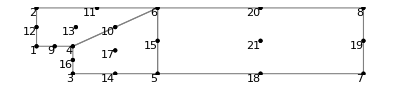

```mathematica
order=2; young=3000*10^3; nu=0.2; eltype=1;
mu=young/(2(1+nu)); lambda=young nu/((1+nu)(1-2nu));
eltype=1;forcing=0.; h=4; 
nnodes={{0,5},{0,12},{6,0},{6,5},{20,0},{20,12},{54,0},{54,12}};
(* 8 points *)
allcoords={{0,5},{0,12},{6,0},{6,5},{20,0},{20,12},{54,0},{54,12}};
(* calcuate points *)
{x1,y1}=allcoords[[1]];{x2,y2}=allcoords[[2]];
{x3,y3}=allcoords[[3]];{x4,y4}=allcoords[[4]];
{x5,y5}=allcoords[[5]];{x6,y6}=allcoords[[6]];
{x7,y7}=allcoords[[7]];{x8,y8}=allcoords[[8]];
{x9,y9}={x1+x4,y1+y4}/2;{x10,y10}={x6+x4,y6+y4}/2;
{x11,y11}={x6+x2,y6+y2}/2;{x12,y12}={x1+x2,y1+y2}/2;
{x13,y13}={x11+x9,y11+y9}/2;
{x14,y14}={x3+x5,y3+y5}/2;{x15,y15}={x6+x5,y6+y5}/2;
{x16,y16}={x4+x3,y3+y4}/2;
{x17,y17}={x15+x16,y15+y16}/2;
{x18,y18}={x7+x5,y7+y5}/2;{x19,y19}={x7+x8,y7+y8}/2;
{x20,y20}={x6+x8,y6+y8}/2;{x21,y21}={x15+x19,y15+y19}/2;
nnodes={{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5},{x6,y6},{x7,y7},{x8,y8},{x9,y9},{x10,y10},{x11,y11},{x12,y12},{x13,y13},{x14,y14},{x15,y15},{x16,y16},{x17,y17},{x18,y18},{x19,y19},{x20,y20},{x21,y21}};
(* 1st element *)
allcoords1={{{x1,y1},{x9,y9},{x4,y4},{x10,y10},{x6,y6},{x11,y11},{x2,y2},{x12,y12},{x13,y13}}};
nnodes1={{x1,y1},{x9,y9},{x4,y4},{x10,y10},{x6,y6},{x11,y11},{x2,y2},{x12,y12},{x13,y13}};
topol1={{1,2,3,4,5,6,7,8,9}};


(* 2nd element *)
allcoords2={{{x3,y3},{x14,y14},{x5,y5},{x15,y15},{x6,y6},{x10,y10},{x4,y4},{x16,y16},{x17,y17}}};
nnodes2={{x3,y3},{x14,y14},{x5,y5},{x15,y15},{x6,y6},{x10,y10},{x4,y4},{x16,y16},{x17,y17}};
topol2={{1,2,3,4,5,6,7,8,9}};


(* 3rd element *)
allcoords3={{{x5,y5},{x18,y18},{x7,y7},{x19,y19},{x8,y8},{x20,y20},{x6,y6},{x15,y15},{x21,y21}}};
nnodes3={{x5,y5},{x18,y18},{x7,y7},{x19,y19},{x8,y8},{x20,y20},{x6,y6},{x15,y15},{x21,y21}};
topol3={{1,2,3,4,5,6,7,8,9}};


(* Visualize *)
meshVis1=Graphics[{FaceForm[],EdgeForm[Gray],GraphicsComplex[nnodes1,Polygon[topol1[[All,{1,2,3,4,5,6,7,8}]]]]}];
meshVis2=Graphics[{FaceForm[],EdgeForm[Gray],GraphicsComplex[nnodes2,Polygon[topol2[[All,{1,2,3,4,5,6,7,8}]]]]}];
meshVis3=Graphics[{FaceForm[],EdgeForm[Gray],GraphicsComplex[nnodes3,Polygon[topol3[[All,{1,2,3,4,5,6,7,8}]]]]}];
nodeVis=Graphics[{Black,PointSize[Medium],Point[nnodes]}];
nodeVis2=Graphics[{MapIndexed[Text[#2[[1]],#1,{2,2}]&,nnodes],{Black,Point[nnodes]}}];
mesh1=Show[meshVis1,meshVis2,meshVis3,nodeVis,nodeVis2]
```

```mathematica
(* calculate golbal stifness *)
allcoords={
{{x1,y1},{x9,y9},{x4,y4},{x10,y10},{x6,y6},{x11,y11},{x2,y2},{x12,y12},{x13,y13}},{{x3,y3},{x14,y14},{x5,y5},{x15,y15},{x6,y6},{x10,y10},{x4,y4},{x16,y16},{x17,y17}},{{x5,y5},{x18,y18},{x7,y7},{x19,y19},{x8,y8},{x20,y20},{x6,y6},{x15,y15},{x21,y21}}
};
nnodes={{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5},{x6,y6},{x7,y7},{x8,y8},{x9,y9},{x10,y10},{x11,y11},{x12,y12},{x13,y13},{x14,y14},{x15,y15},{x16,y16},{x17,y17},{x18,y18},{x19,y19},{x20,y20},{x21,y21}};
topol={
{1,9,4,10,6,11,2,12,13},
{3,14,5,15,6,10,4,16,17},
{5,18,7,19,8,20,6,15,21}};
{kE,fE}=Assemble[allcoords,nnodes,topol,order,eltype,h];
```

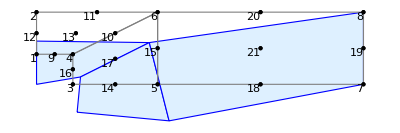

(0
-0.00625214
0
-0.00601777
0.00087788
-0.00579312
0.00157933
-0.00472293
0.00236955
-0.00759255
-0.00171435
-0.00632669
0
0
0
0
-0.000493413
-0.00712497
0.000352892
-0.000863997
0.000126387
-0.00657394
0
-0.00644448
-0.000613785
-0.00551498
-0.000278302
-0.00132166
0.00206457
-0.007342
-0.000609237
-0.00762662
0.00219534
-0.00313996
0.00610813
-0.00272202
0
0
0.000528551
-0.00301669
-0.00108853
-0.00315765)

```mathematica
FE=ApplyNodeBCForce[fE,{2,6,11},{{0,-666.6666666666663},{0,-666.6666666666665},{0,-2666.666666666667}}];
FE=ApplyNodeBCForce[FE,{6,8,20},{{0,-1133.3333333333326},{0,-1133.333333333333},{0,-4533.333333333332}}];
BIG=10^12;
KE=ApplyNodeBCDisplacement[kE,{7,8,19},{{{BIG,1},{1,BIG}},{{BIG,1},{1,BIG}},{{BIG,1},{1,BIG}}}];
KE=ApplyNodeBCDisplacement[KE,{1,2,12},{{{BIG,1},{1,1}},{{BIG,1},{1,1}},{{BIG,1},{1,1}}}];
sol=LinearSolve[KE,FE,Method->"Pardiso"];
scale=800;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=Table[{deformed[[i]],deformed[[i+1]]},{i,1,Length[deformed],2}];
topol={
{1,9,4,10,6,11,2,12,13},
{3,14,5,15,6,10,4,16,17},
{5,18,7,19,8,20,6,15,21}};
meshVisDef=Graphics[{FaceForm[{LightBlue,Opacity[3]}],EdgeForm[{Dashed,Blue}],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,3,5,7}]]]]}];
Show[meshVisDef,mesh1]
 d=sol//Chop;
```

```mathematica
u =100*d;(*scale factor = 100*)
NewNodes=Table[{nnodes⟦i,1⟧+u⟦2i-1⟧,nnodes⟦i,2⟧+u⟦2i⟧},{i,1,Length[nnodes]}];
lm[1]={1,2,17,18,7,8,19,20,11,12,21,22,3,4,23,24};lm[2]={5,6,29,30,9,10,31,32,11,12,19,20,7,8,27,28};lm[3]={9,10,35,36,13,14,37,38,15,16,39,40,11,12,31,32};
topol={
{1,9,4,10,6,11,2,12},
{3,14,5,15,6,10,4,16},
{5,18,7,19,8,20,6,15}};
```

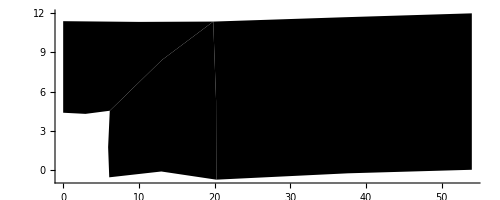

```mathematica
(* Ux displacement *)
Show[Graphics[
Polygon[
NewNodes[[topol[[1]]]],VertexColors->Hue/@u[[lm[1]]][[;;;;2]]],Axes->True],
Graphics[
Polygon[
NewNodes[[topol[[2]]]],VertexColors->Hue/@u[[lm[2]]][[;;;;2]]],Axes->True],
Graphics[
Polygon[
NewNodes[[topol[[3]]]],VertexColors->Hue/@u[[lm[3]]][[;;;;2]]],Axes->True]
]
```

```mathematica
(* Uy displacement *)
Show[Graphics[
Polygon[
NewNodes[[topol[[1]]]],VertexColors->Hue/@u[[lm[1]]][[2;;;;2]]],Axes->True],

Graphics[
Polygon[
NewNodes[[topol[[2]]]],VertexColors->Hue/@u[[lm[2]]][[2;;;;2]]],Axes->True],
Graphics[
Polygon[
NewNodes[[topol[[3]]]],VertexColors->Hue/@u[[lm[3]]][[2;;;;2]]],Axes->True]
]
```

-Graphics-